# Potential lowering

## Cartoon

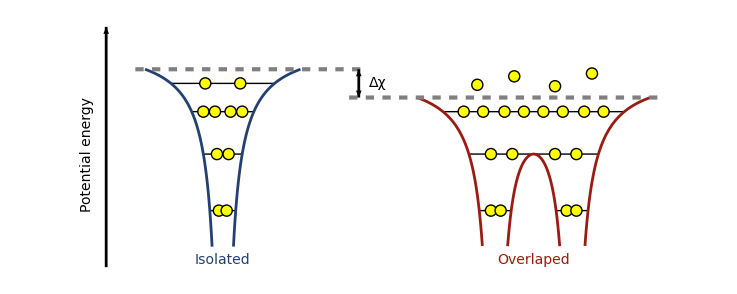

```mathematica
(* -- potential functions -- *)
f0[x_]:=-8/x+2;
f1[x_]:=Which[
-4≤x<0,f0[-x],
0<x≤4,f0[x]
];
f2[x_]:=Which[
-6≤x<-2,f0[-(x+2)]-2,
-2≤x<2,f0[x+2]+f0[-(x-2)]-2,
2≤x<6,f0[x-2]-2
];

(* -- discrete data points -- *)
isolated[x_]:=f1[x-8];
overlaped[x_]:=f2[x-24];
dt={
Table[{x,isolated[x]},{x,4,7.45,.01}],
Table[{x,isolated[x]},{x,8.55,12,.01}],
Table[{x,overlaped[x]},{x,18,21.36,.01}],
Table[{x,overlaped[x]},{x,22.66,25.34,.01}],
Table[{x,overlaped[x]},{x,26.64,30,.01}]
};

(* -- levels -- *)
isolatedLevels=Table[{#,lv}&/@(Sort[Solve[isolated[x]==lv,x][[All,1,2]],#1<#2&]),{lv,{-10,-6,-3,-1}}];
overlapedLevels=Table[{#,lv}&/@(Sort[Solve[overlaped[x]==lv,x][[All,1,2]],#1<#2&]),{lv,{-10,-6,-3}}];
levels=Join[isolatedLevels,Partition[overlapedLevels[[1]],2],overlapedLevels[[2;;]]];

(* -- electrons -- *)
pts={{7.8,-10},{8.2,-10},
{7.7,-6},{8.3,-6},
{7,-3},{7.6,-3},{8.4,-3},{9,-3},
{7.1,-1},{8.9,-1},
{21.8,-10},{22.3,-10},{25.7,-10},{26.2,-10},
{21.8,-6},{22.9,-6},{25.1,-6},{26.2,-6},
{20.4,-3},{21.4,-3},{22.5,-3},{23.5,-3},{24.5,-3},{25.5,-3},{26.6,-3},{27.6,-3},
{21.1,-1.1},{23,-.5},{25.1,-1.2},{27,-.3}
};

(* -- plot -- *)
gf=ListLinePlot[

dt,

Prolog->{{Black,AbsoluteThickness[1],Line[levels]}},

Epilog->{
{Black,AbsoluteThickness[2],Arrowheads[{0,.04}],Arrow[{{2,-14},{2,3}}]},
Text[Style["Isolated",FontColor->RGBColor[.14,.25,.44,1],FontSize->14,FontWeight->Plain],{8,-14},{0,-1}],
Text[Style["Overlaped",FontColor->RGBColor[.60,.11,.07,1],FontSize->14,FontWeight->Plain],{24,-14},{0,-1}],
{EdgeForm[{Black,AbsoluteThickness[1]}],FaceForm[{Yellow}],Disk[#,Offset[4]]}&/@pts,
{Gray,AbsoluteThickness[3],AbsoluteDashing[6],Line[{{3.5,0},{15.5,0}}]},
{Gray,AbsoluteThickness[3],AbsoluteDashing[6],Line[{{14.5,-2},{30.5,-2}}]},
{Black,AbsoluteThickness[2],Arrowheads[{-.015,.015}],Arrow[{{15,-2},{15,0}}]},
Text[Style["Δχ",FontColor->Black,FontSize->14,FontWeight->Plain],{15.5,-1},{-1,0}],
Text[Style["Potential energy",FontColor->Black,FontSize->14,FontWeight->Plain],{1,-6},{0,0},{0,1}]
},

Joined->True,
PlotRange->{{0,31},{-14,3}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},

PlotStyle->{
{RGBColor[.14,.25,.44,1],Opacity[1],AbsoluteThickness[2]},
{RGBColor[.14,.25,.44,1],Opacity[1],AbsoluteThickness[2]},
{RGBColor[.60,.11,.07,1],Opacity[1],AbsoluteThickness[2]},
{RGBColor[.60,.11,.07,1],Opacity[1],AbsoluteThickness[2]},
{RGBColor[.60,.11,.07,1],Opacity[1],AbsoluteThickness[2]},
{RGBColor[.60,.11,.07,1],Opacity[1],AbsoluteThickness[2]}
},

Axes->False,
Frame->False,
GridLines->None,

ImagePadding->0,
ImageSize->(130*2)*(72/25.4),
AspectRatio->.4

];

Print[gf];

Export[NotebookDirectory[]<>"continuumLowering.pdf",gf];
```